```mathematica
ClearAll[ sol,kappa,P, P1,P2,y0,ymax,T0,A,L,Ltri,x,y,z,z0,s,Xc,Yc,Rc,Rh,powerDensity3D,powerDensityFun3D,cpsInterFunc,copperCylinderRegion,missingArcRegion,missingBeamCylinder,meshRegion]
```

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
cpsInterFunc=Import["/home/hovanes/Documents/Wolfram\ Mathematica/klcps_31b.m"]
```

InterpolatingFunction[{{0.0125, 5.9875}, {-5.21417, 1.02538}, {0.25, 93.75}}, <>]

```mathematica
kappa=0.00385;P=52;P1=1;P2=1.5;y0=0.3;ydat=6;ymax=10;T0=70;L=90;Ltri=54;z0=L/2.;s=20;
Xc=0;Yc=2;
Rc=8; Rh=1;
```

```mathematica
powerDensity3D[x_,y_,z_]=Piecewise[{{cpsInterFunc[y,x,z]/1000,y<ydat}},0.00001]
```

Piecewise[{{(InterpolatingFunction[{{0.0125, 5.9875}, {-5.21417, 1.02538}, {0.25, 93.75}}, <>][y,x,z])/1000, y<6}, {0.00001, True}}]

```mathematica
(*NIntegrate[y*powerDensity3D[x,y,z],{x,-5*Pi/3,Pi/3},{y,0,ymax},{z,0,L},WorkingPrecision->9]*)
```

InterpolatingFunction::dmval: Input value {0.000714286,-(2 π)/3,1.00636} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.,-(2 π)/3,89.2054} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.,-(2 π)/3,88.808} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

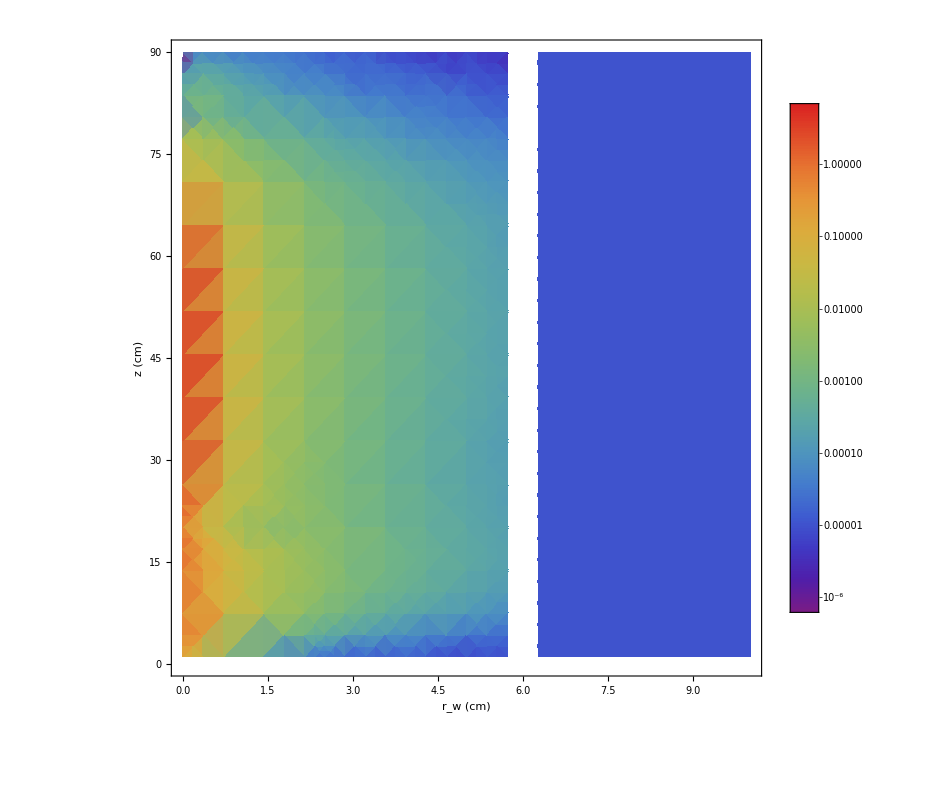

```mathematica
DensityPlot[powerDensity3D[-2*Pi/3,y,z],{y,0.0,ymax},{z,1,L},ColorFunction->{"Rainbow"},PlotRange->Automatic,PlotLegends->Automatic, ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"r_w (cm)", "z (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

InterpolatingFunction::dmval: Input value {0.3,-4.18879,0.00183857} lies outside the range of data in the interpolating function. Extrapolation will be used.

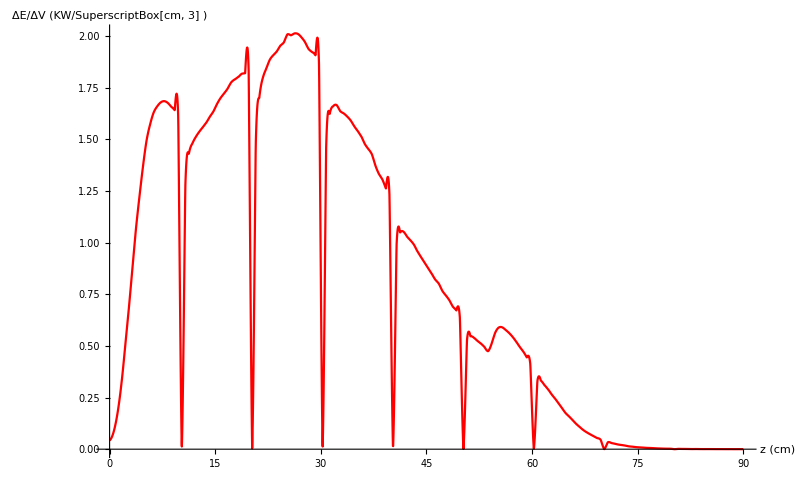

```mathematica
Plot[powerDensity3D[-4.0*Pi/3,0.3,z],{z,0,L}, AxesLabel->{"z (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.002]}]
```

InterpolatingFunction::dmval: Input value {0.000714286,-5.23554,45.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.19643,-5.23599,45.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.24107,-5.23599,45.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

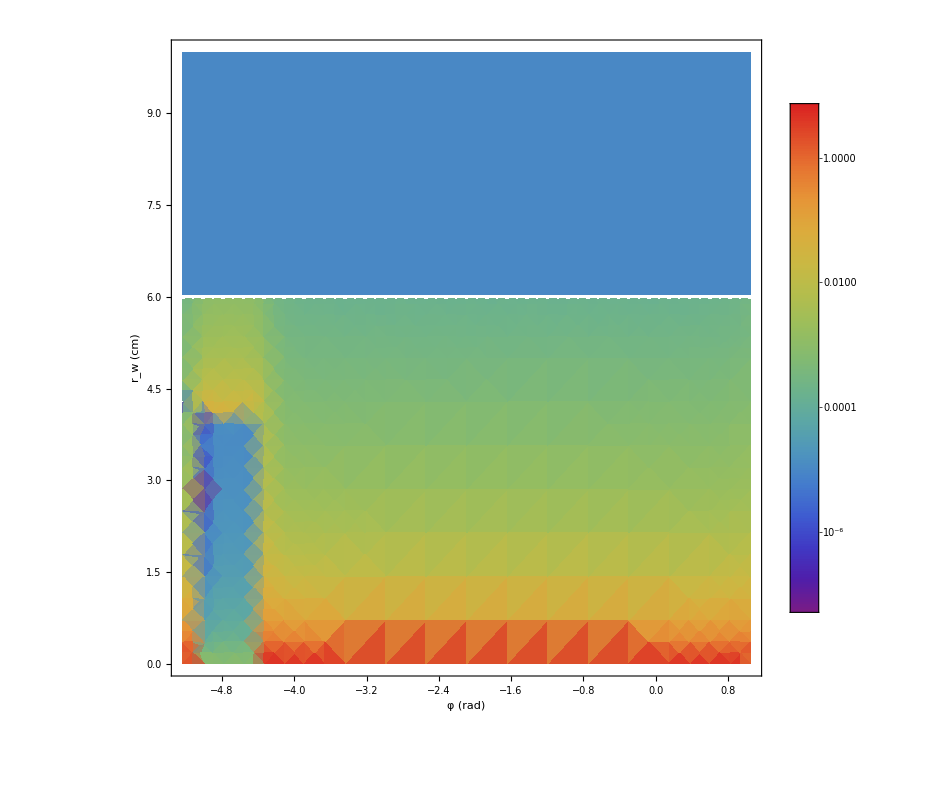

```mathematica
DensityPlot[powerDensity3D[x,y,z0],{x,-5*Pi/3,Pi/3},{y,0.0,ymax},ColorFunction->"Rainbow",PlotRange->Automatic,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"φ (rad)", "r_w (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

InterpolatingFunction::dmval: Input value {0.000714286,-5.23554,55} lies outside the range of data in the interpolating function. Extrapolation will be used.

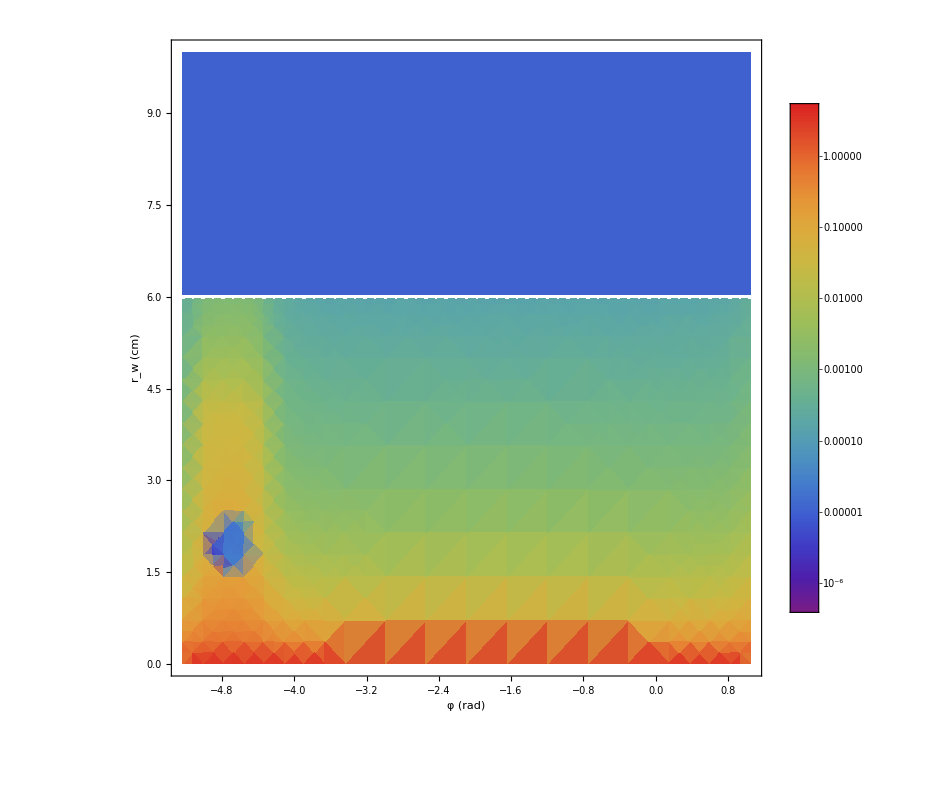

```mathematica
DensityPlot[powerDensity3D[x,y,55],{x,-5*Pi/3,Pi/3},{y,0.0,ymax},ColorFunction->"Rainbow",PlotRange->Automatic,PlotLegends->Automatic,ScalingFunctions->{Identity,Identity,"Log"},ImageSize->{800,800},FrameLabel->{"φ (rad)", "r_w (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

InterpolatingFunction::dmval: Input value {0.000122571,-π/3,55} lies outside the range of data in the interpolating function. Extrapolation will be used.

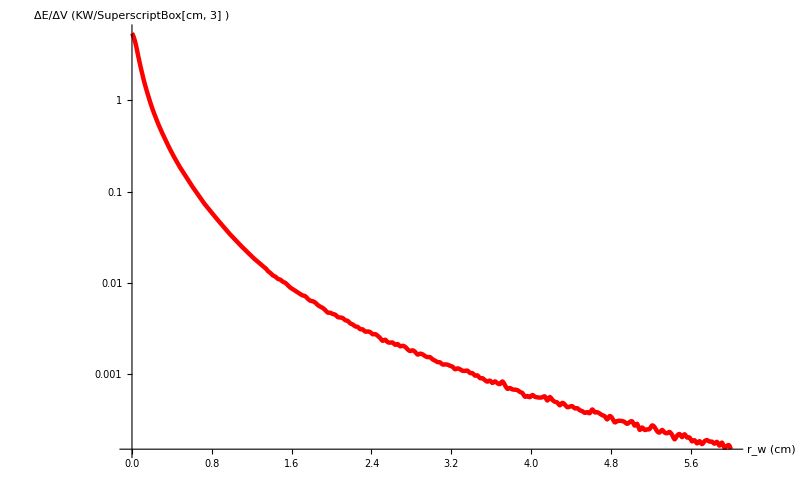

```mathematica
LogPlot[powerDensity3D[-Pi/3,y,55],{y,0,ydat},AxesLabel->{"r_w (cm)", "ΔE/ΔV (KW/SuperscriptBox[cm, 3] )"} ,LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500},PlotRange->Full, PlotStyle->{Red,Thickness[0.004]}]
```

```mathematica
copperCylinderRegion=ImplicitRegion[((y*Sin[x]-Yc)^2+(y*Cos[x])^2)<=Rc^2,{{x,-5*Pi/3,Pi/3},{y,0,ymax},{z,0,L}}];
```

```mathematica
RegionPlot3D[copperCylinderRegion, Mesh->Full]
```

```mathematica
missingArcRegion=ImplicitRegion[y≤(Rc*Sin[-4*Pi/3]/Sin[x]),{{x,-5*Pi/3,-4*Pi/3},{y,0,ymax},{z,0,Ltri}}];
```

```mathematica
missingBeamCylinder=ImplicitRegion[((y*Sin[x]-Yc)^2+(y*Cos[x])^2)<=Rh^2,{{x,-5*Pi/3,Pi/3},{y,0,ymax},{z,Ltri,L}}];
```

```mathematica
copperRegion = RegionDifference[copperCylinderRegion,RegionUnion[missingArcRegion,missingBeamCylinder]];
```

```mathematica
RegionPlot3D[copperRegion]
```

-Graphics3D-

```mathematica
(*copperRegion=ImplicitRegion[((y*Sin[x]-Yc)^2+(y*Cos[x])^2)<=Rc^2,{{x,-4*Pi/3,Pi/3},{y,0,ymax},{z,0,L}}];*)
```

```mathematica
meshRegion=ToElementMesh[copperRegion,MeshQualityGoal->"Maximal"];
RegionPlot3D[copperRegion, Mesh->All]
```

-Graphics3D-

```mathematica
(*eqn=-Laplacian[u[x,y,z],{y,x,z},"Cylindrical"]==1/kappa*powerDensity3D[x,y,z]+NeumannValue[0.0,x==-4*Pi/3||x==Pi/3]+NeumannValue[0.0,z==0||z==L];*)
```

```mathematica
eqn=-Laplacian[u[x,y,z],{y,x,z},"Cylindrical"]==1/kappa*powerDensity3D[x,y,z]+ NeumannValue[0.0,{x,y,z}∈RegionBoundary@ missingBeamCylinder] +NeumannValue[0.0,{x,y,z}∈RegionBoundary@ missingArcRegion ];
```

```mathematica
sol=NDSolveValue[{eqn,DirichletCondition[u[x,y,z]==T0,((y*Sin[x]-Yc)^2+(y*Cos[x])^2==Rc^2)]}, u,{x, y,z} ∈ meshRegion]
```

InterpolatingFunction[{{-5.23599, 1.0472}, {0., 9.96207}, {0., 90.}}, <>]

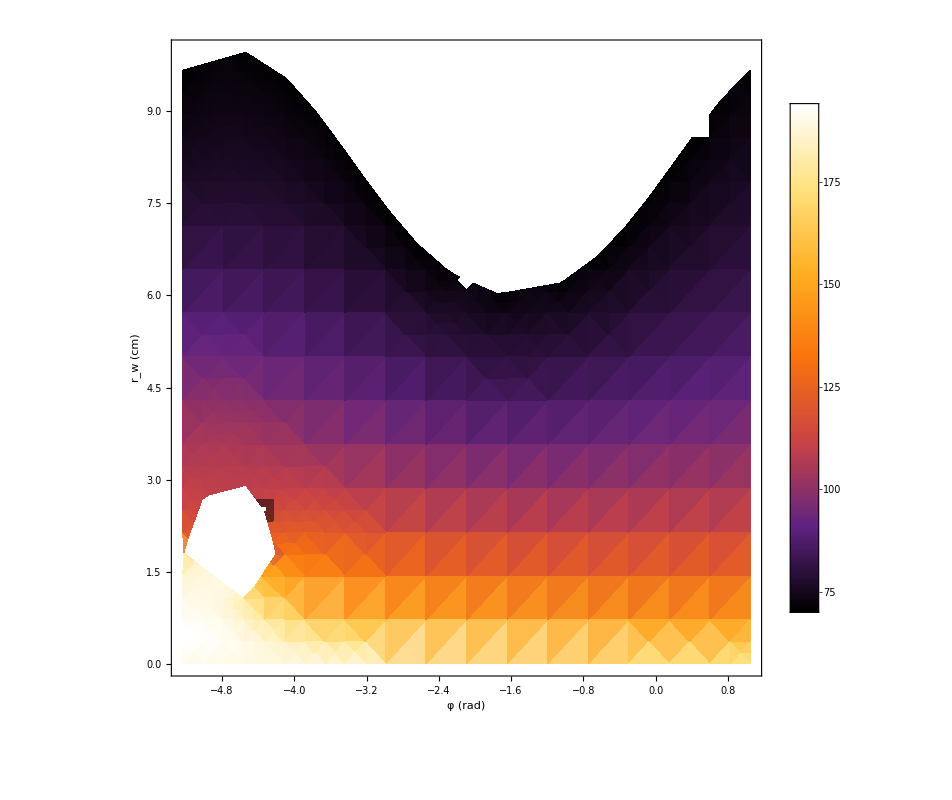

```mathematica
DensityPlot[sol[x,y,55], {x,-5*Pi/3,Pi/3},{y,0,ymax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,200},ImageSize->{800,800},FrameLabel->{"φ (rad)", "r_w (cm)", "T (^oC)"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

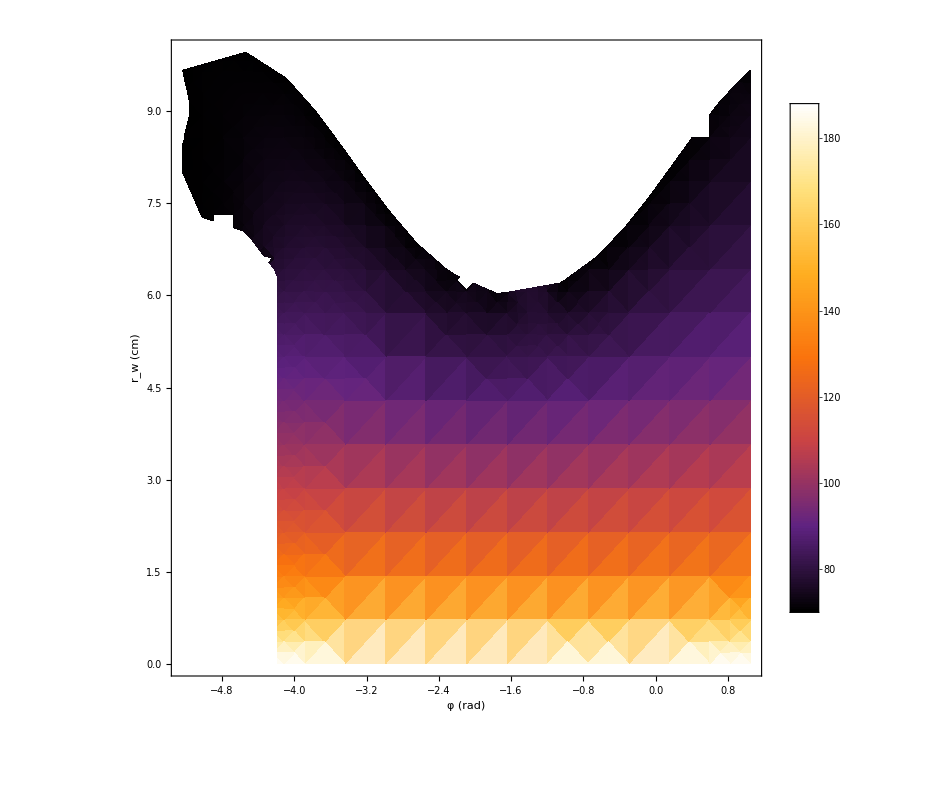

```mathematica
DensityPlot[sol[x,y,45], {x,-5*Pi/3,Pi/3},{y,0,ymax},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,200},ImageSize->{800,800},FrameLabel->{"φ (rad)", "r_w (cm)", "T (^oC)"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

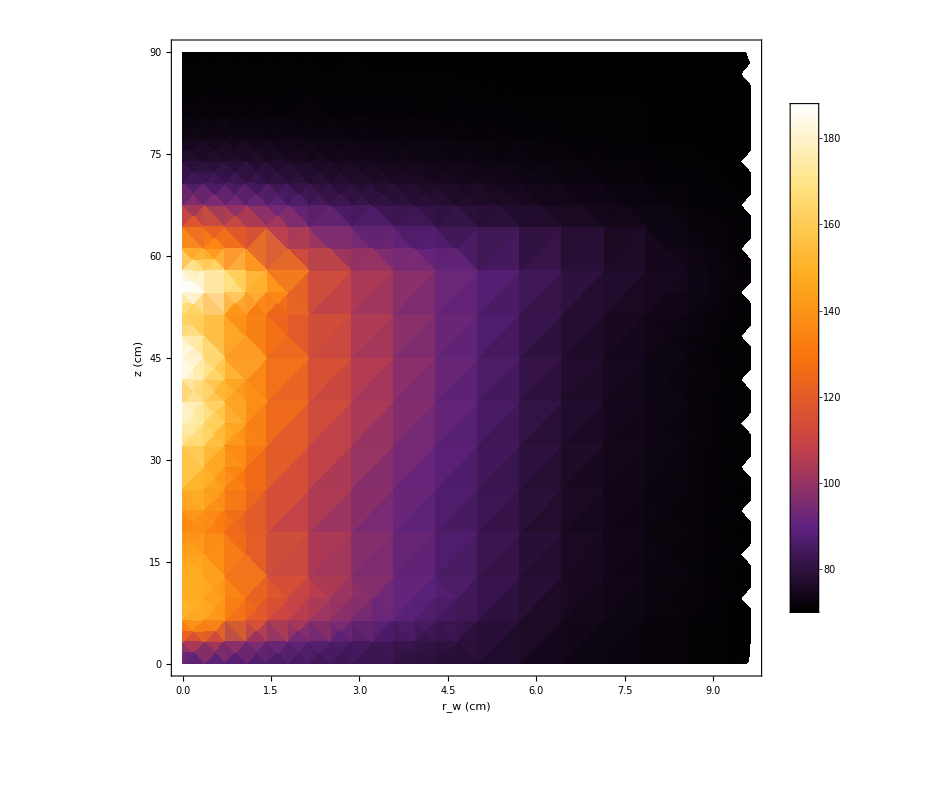

```mathematica
DensityPlot[sol[-4.*Pi/3,y,z], {y,0,ymax},{z,0,L},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,200},ImageSize->{800,800},FrameLabel->{ "r_w (cm)", "z (cm)","T (^oC)"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

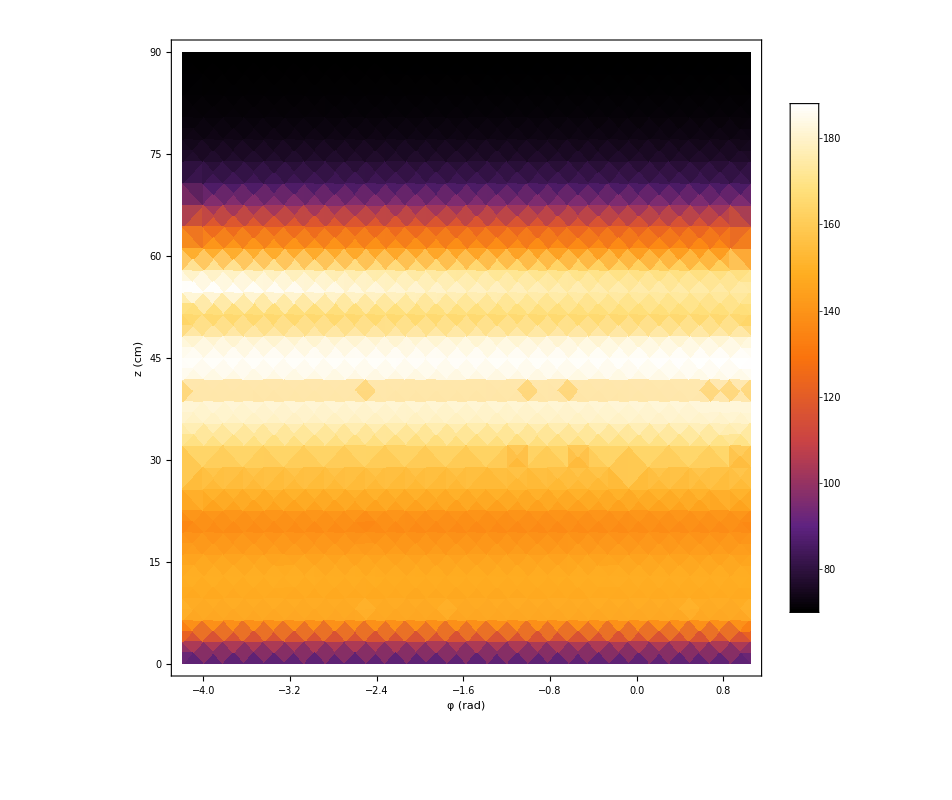

```mathematica
DensityPlot[sol[x,0.,z],{x,-4*Pi/3,Pi/3} ,{z,0,L},ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotRange->{T0,200},ImageSize->{800,800},FrameLabel->{ "φ (rad)", "z (cm)","T (^oC)"} , LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->1]
```

```mathematica
SliceContourPlot3D[sol[x,y,z], "CenterPlanes",{x,-4*Pi/3,Pi/3},{y,0,ymax},{z,0,L}, PlotTheme->"Detailed", ImageSize->{800,800},PlotLabel->"T (^oC)",AxesLabel->{ "φ (rad)", "r_w (cm)","z (cm)"},LabelStyle->{17,GrayLevel[0],Italic}]
```

-Graphics3D-

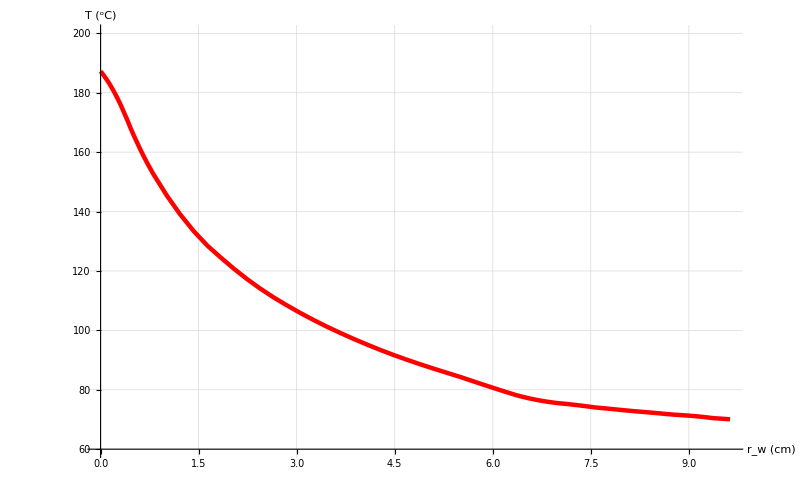

```mathematica
Plot[sol[-4*Pi/3,y,45], {y,0.0,ymax},GridLines->Automatic,PlotRange->{T0-10,200},AxesLabel->{"r_w (cm)", "T (^oC)"} ,LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

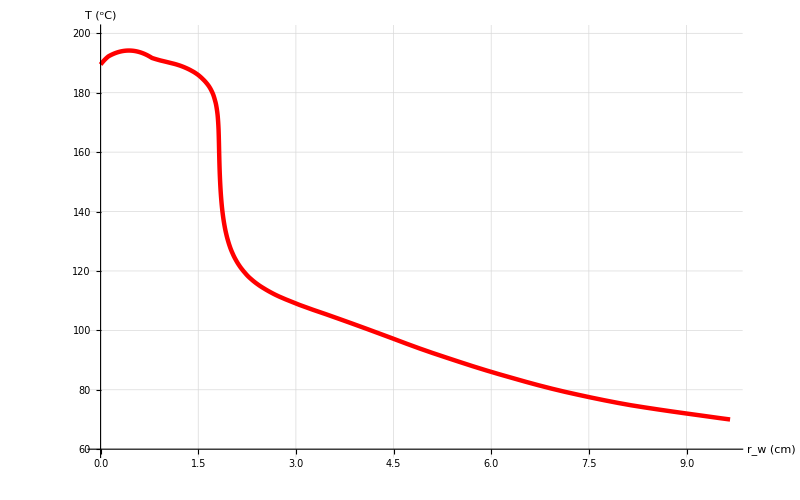

```mathematica
Plot[sol[-5*Pi/3,y,55], {y,0.0,ymax},GridLines->Automatic,PlotRange->{T0-10,200},AxesLabel->{"r_w (cm)", "T (^oC)"} ,LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

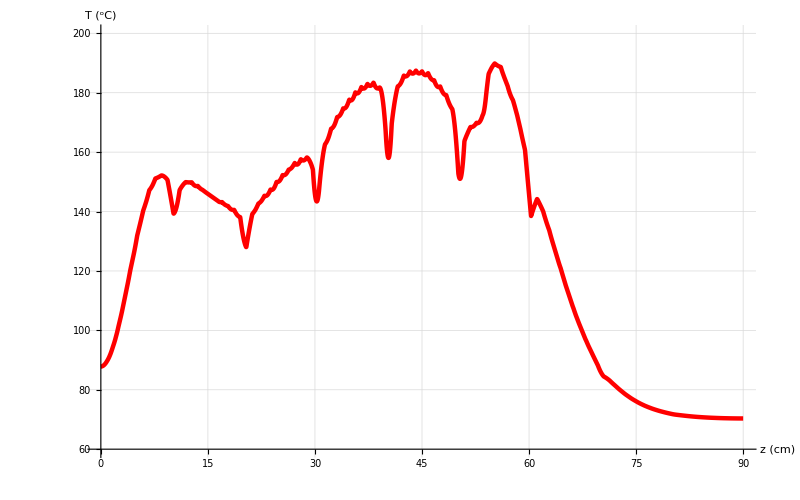

```mathematica
Plot[sol[-4.*Pi/3,0.,z], {z,0.0,L},GridLines->Automatic,PlotRange->{T0-10,200},AxesLabel->{"z (cm)", "T (^oC)"} ,LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```

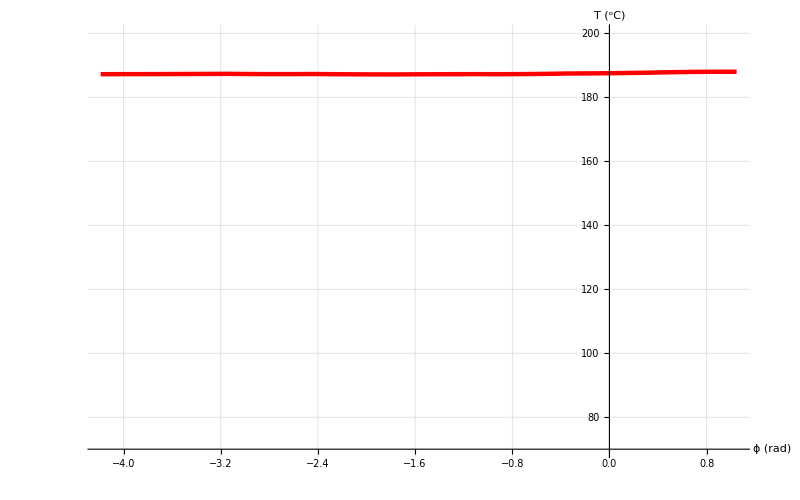

```mathematica
Plot[sol[x,0.,45], {x,-4*Pi/3,Pi/3},GridLines->Automatic,PlotRange->{T0,200},AxesLabel->{"ϕ (rad)", "T (^oC)"} ,LabelStyle->{17,GrayLevel[0],Italic},AspectRatio->Full,ImageSize->{800,500}, PlotStyle->{Red,Thickness[0.004]}]
```